```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\flux_pmf\xin\PVP20\100Ag\equilibrate\1_NVT

```mathematica
numbatom=33882;
numbatomtype = 16;
```

```mathematica
masslist={1.008,1.008,1.008,1.008,12.011,12.011,12.011,12.011,12.011,14.007,15.9994,1.008,1.008,12.011,15.9994,107.8682};
```

```mathematica
masslist[[11]] (*Atom type of O in PVP molecule*)
```

15.9994

```mathematica
trajfilename="traj_npt.lammpstrj"
```

traj_npt.lammpstrj

```mathematica
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"]
```

ITEM: TIMESTEP

```mathematica
timestep=Read[traj,Number]
timesteptemp=timestep;
```

0

```mathematica
timeprod=2000;
timestepthermo=2000;
timesteptraj=10000;
(*Production time*)
```

```mathematica
(*Atoms per molecules, PVP10 = 175, PVP = 90, 2PDO = 13, MB3 = 16, EPD = 19*)
(*DON'T FORGET TO MANUALLY EDIT EVERYTIME*)
sizepvp=345;
numbpvp=10;
```

```mathematica
firstpvpatomid=1;
lastpvpatomid=3450;
```

```mathematica
lz=86.5788933385011;
```

```mathematica
(*pvpatomtypeseq={10,8,8,11,9,10,8,8,11,9};*)
```

```mathematica
pvpatomtypeseq={8,4,4,4,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,8,4,4,4,6,2,10,5,11,9,1,1,9,1,1,9,1,1};
```

```mathematica
Length[pvpatomtypeseq]
```

345

```mathematica
oxypos=Flatten[Position[pvpatomtypeseq,11]]
```

{12,29,46,63,80,97,114,131,148,165,182,199,216,233,250,267,284,301,318,336}

```mathematica
masslist[[pvpatomtypeseq]]
```

{12.011,1.008,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,1.008,12.011,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008}

```mathematica
masslistrep=Flatten[Table[masslist[[pvpatomtypeseq]],{i,numbpvp}]];
```

```mathematica
IfBelow[x_]:=If[x<0,1,0];
IfAbove[x_]:=If[x>lz,-1,0];
```

```mathematica
oxy=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
pvppositiontemp=atompositiontemp[[firstpvpatomid;;lastpvpatomid]];
pvppositiontemp[[All,7]]=pvppositiontemp[[All,9]]*lz+pvppositiontemp[[All,6]];
oxytemp=Partition[pvppositiontemp[[All,7]],sizepvp][[All,oxypos]];
Sow[oxytemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];//AbsoluteTiming
```

{63.41063,Null}

```mathematica
timesteptemp2
```

4150000

```mathematica
Close[traj];
```

```mathematica
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"]
```

ITEM: TIMESTEP

```mathematica
timestep=Read[traj,Number]
timesteptemp=timestep;
```

0

```mathematica
firstagatomid=26971;
lastagatomid=33881;
```

```mathematica
agposition=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
agpositiontemp=atompositiontemp[[firstagatomid;;lastagatomid]];
agpositiontemp[[All,7]]=agpositiontemp[[All,9]]*lz+agpositiontemp[[All,6]];
Sow[agpositiontemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];//AbsoluteTiming
```

{73.76122,Null}

```mathematica
agposition=Partition[Flatten[agposition],9];
```

```mathematica
(*Density profile*)
```

```mathematica
agz=agposition[[All,7]];
```

```mathematica
(* pvpcom *)
(* com-z of each pvp molecules at each timestep *)
(* arranged in order of pvp1timestep1, ..., pvp18timestep1, pvp1timestep2, ..., pvp18timestep2, ..., pvp18timestepend *)
```

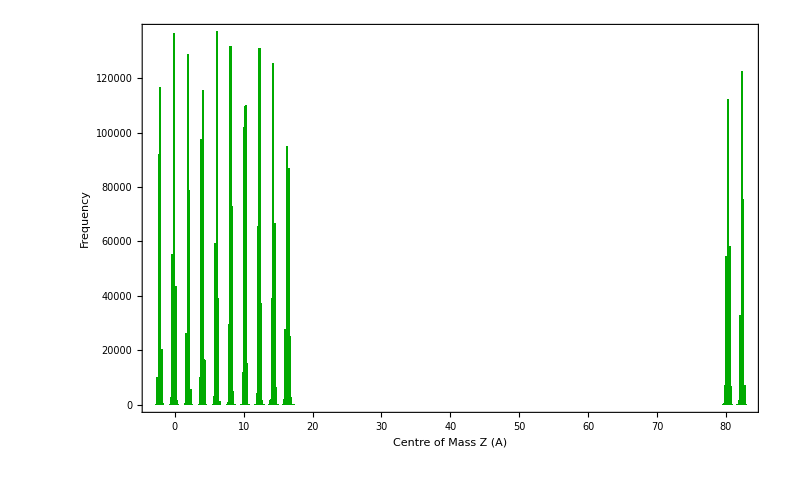

```mathematica
AgComzHist=Histogram[agz,300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
topAgsurface=Nearest[agz,20][[1]]
```

17.4065

```mathematica
oxyfromsurf=oxy-topAgsurface;
```

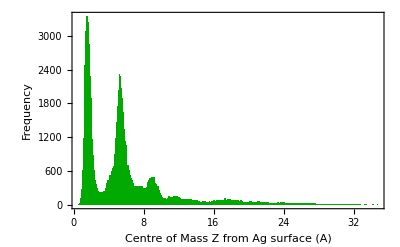

```mathematica
ComzHist=Histogram[Flatten[oxyfromsurf],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
CreateDirectory["density"];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\flux_pmf\\xin\\PVP20\\100Ag\\equilibrate\\1_NVT\\density\\" already exists.

```mathematica
Export["density/Histogram.png",ComzHist,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["density/Histogram.png"]]]
```

```mathematica
SetDirectory["D:/tonnam_backup/Research_scratch/flux_pmf/xin/PVP20/111Ag/equilibrate/1_NVT"]
```

D:\tonnam_backup\Research_scratch\flux_pmf\xin\PVP20\111Ag\equilibrate\1_NVT

```mathematica
numbatom=35035;
numbatomtype = 16;
```

```mathematica
masslist={1.008,1.008,1.008,1.008,12.011,12.011,12.011,12.011,12.011,14.007,15.9994,1.008,1.008,12.011,15.9994,107.8682};
```

```mathematica
masslist[[11]] (*Atom type of O in PVP molecule*)
```

15.9994

```mathematica
trajfilename="traj_npt.lammpstrj"
```

traj_npt.lammpstrj

```mathematica
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"]
```

ITEM: TIMESTEP

```mathematica
timestep=Read[traj,Number]
timesteptemp=timestep;
```

0

```mathematica
timeprod=2000;
timestepthermo=2000;
timesteptraj=10000;
(*Production time*)
```

```mathematica
(*Atoms per molecules, PVP10 = 175, PVP = 90, 2PDO = 13, MB3 = 16, EPD = 19*)
(*DON'T FORGET TO MANUALLY EDIT EVERYTIME*)
sizepvp=345;
numbpvp=10;
```

```mathematica
firstpvpatomid=1;
lastpvpatomid=3450;
```

```mathematica
lz=89.372846752191;
```

```mathematica
(*pvpatomtypeseq={10,8,8,11,9,10,8,8,11,9};*)
```

```mathematica
pvpatomtypeseq={8,4,4,4,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,6,2,7,3,3,10,5,11,9,1,1,9,1,1,9,1,1,8,4,4,4,6,2,10,5,11,9,1,1,9,1,1,9,1,1};
```

```mathematica
Length[pvpatomtypeseq]
```

345

```mathematica
oxypos=Flatten[Position[pvpatomtypeseq,11]]
```

{12,29,46,63,80,97,114,131,148,165,182,199,216,233,250,267,284,301,318,336}

```mathematica
masslist[[pvpatomtypeseq]]
```

{12.011,1.008,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,12.011,1.008,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008,1.008,12.011,1.008,14.007,12.011,15.9994,12.011,1.008,1.008,12.011,1.008,1.008,12.011,1.008,1.008}

```mathematica
masslistrep=Flatten[Table[masslist[[pvpatomtypeseq]],{i,numbpvp}]];
```

```mathematica
IfBelow[x_]:=If[x<0,1,0];
IfAbove[x_]:=If[x>lz,-1,0];
```

```mathematica
oxy111=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
pvppositiontemp=atompositiontemp[[firstpvpatomid;;lastpvpatomid]];
pvppositiontemp[[All,7]]=pvppositiontemp[[All,9]]*lz+pvppositiontemp[[All,6]];
oxytemp=Partition[pvppositiontemp[[All,7]],sizepvp][[All,oxypos]];
Sow[oxytemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];//AbsoluteTiming
```

{61.56752,Null}

```mathematica
timesteptemp2
```

3860000

```mathematica
Close[traj];
```

```mathematica
traj=OpenRead[trajfilename];
Find[traj,"TIMESTEP"]
```

ITEM: TIMESTEP

```mathematica
timestep=Read[traj,Number]
timesteptemp=timestep;
```

0

```mathematica
firstagatomid=26971;
lastagatomid=35034;
```

```mathematica
agposition=Reap[
While[!(timesteptemp===EndOfFile),
Find[traj,"ATOMS id mol type"];
atompositiontemp=Sort[ReadList[traj,{Number,Number,Number,Number,Number,Number, Number,Number,Number},numbatom]];
atompositiontemp[[All,1]]=timesteptemp;
agpositiontemp=atompositiontemp[[firstagatomid;;lastagatomid]];
agpositiontemp[[All,7]]=agpositiontemp[[All,9]]*lz+agpositiontemp[[All,6]];
Sow[agpositiontemp];
timestepdiff=timesteptemp-timesteptemp2;
timesteptemp2=timesteptemp;
Find[traj,"TIMESTEP"];
timesteptemp = Read[traj,Number];
]
][[2,1]];//AbsoluteTiming
```

{56.05121,Null}

```mathematica
agposition=Partition[Flatten[agposition],9];
```

```mathematica
(*Density profile*)
```

```mathematica
agz=agposition[[All,7]];
```

```mathematica
(* pvpcom *)
(* com-z of each pvp molecules at each timestep *)
(* arranged in order of pvp1timestep1, ..., pvp18timestep1, pvp1timestep2, ..., pvp18timestep2, ..., pvp18timestepend *)
```

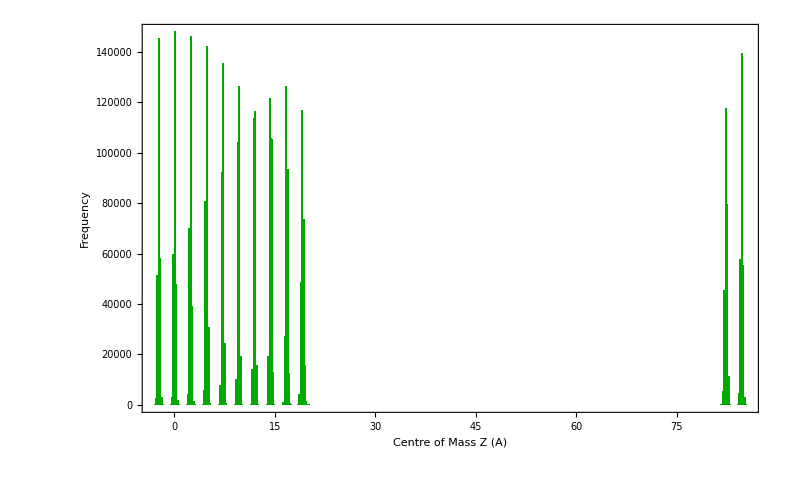

```mathematica
AgComzHist=Histogram[agz,300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
topAgsurface=Nearest[agz,20][[1]]
```

20.0012

```mathematica
oxyfromsurf111=oxy111-topAgsurface;
```

```mathematica
ComzHist=Histogram[Flatten[oxyfromsurf],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

-Graphics-

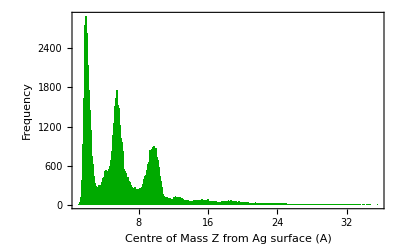

```mathematica
ComzHist=Histogram[Flatten[oxyfromsurf111],300,ChartStyle->Darker[Green],Frame->True,FrameLabel->{"Centre of Mass Z from Ag surface (A)","Frequency"},LabelStyle->Directive[FontSize->15]]
```

```mathematica
CreateDirectory["density"];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\flux_pmf\\xin\\PVP20\\111Ag\\equilibrate\\1_NVT\\density\\" already exists.

```mathematica
Export["density/Histogram.png",ComzHist,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["density/Histogram.png"]]]
```

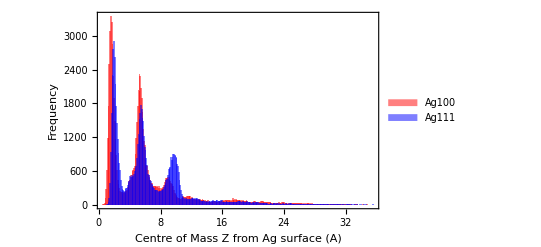

```mathematica
ComzHistComp=Histogram[{Flatten[oxyfromsurf],Flatten[oxyfromsurf111]},
300,
ChartStyle->{Red,Blue},
ChartLegends->Placed[{"Ag100","Ag111"},Bottom],
Frame->True,
FrameLabel->{"Centre of Mass Z from Ag surface (A)","Frequency"},
LabelStyle->Directive[FontSize->15]]
```

```mathematica
Export["density/Histogram_Compare.png",ComzHistComp,ImageResolution->300];
```